```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/BRETT-STUFF

### Step function model

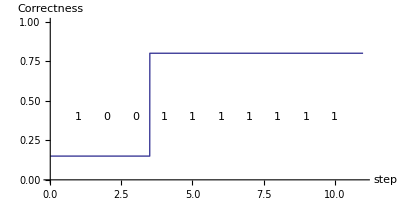

```mathematica
stepPlot=Block[{l=3.5,pg=.15,ps=0.2},Plot[If[x<l,pg,1-ps],{x,0,11},PlotRange->{0,1},Epilog->{Table[Text[If[x<l,If[RandomReal[]>pg,0,1],If[RandomReal[]<ps,0,1]],{x,.4}],{x,1,10}]},AxesLabel->{"step","Correctness"},BaseStyle->{FontSize->12}, AspectRatio->1/2]]
```

```mathematica
Export["step.eps",stepPlot]
```

step.eps